```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/tep/Documents/tex_bulge/code/nb

## Growth rate

#### Import data

#### Diffusion coefficients

```mathematica
(*tabqx=Import["../data/Dump_Growth_Rate_Rotation_eps0_1_precise.hf5",{"Datasets","tabqx"}];
tabGR=Import["../data/Dump_Growth_Rate_Rotation_eps0_1_precise.hf5",{"Datasets","tabGR"}]; *)
tabqx=Import["../data/Dump_Growth_Rate_Rotation_eps0_1.hf5",{"Datasets","tabqx"}];
tabGR=Import["../data/Dump_Growth_Rate_Rotation_eps0_1.hf5",{"Datasets","tabGR"}]; 

GRTable=Partition[{tabqx,tabGR}//Transpose//Flatten,3];
a=GRTable[[All,1]];
b=GRTable[[All,2]];
GRTable[[All,2]]=a;
GRTable[[All,1]]=b;
```

#### Plot data

```mathematica
(*Generic options for the plots.*)
fontname = "Didot";
fontsize = 12;
basestyleplot = {FontFamily -> fontname,FontSize->fontsize};
labelstyleplot = {FontFamily -> fontname, FontSize -> fontsize};
imagesize = Large;(*350;*)
(*Making the plot.*)
(*Range of the plot.*)
qmin = 0.5;
qmax =1.0;
xmin = 0.0;
xmax = 0.4;
zmin =0;
zmax = 2;
(*Axes of the plot.*)
ax = Row[{Style["q = ",fontname,fontsize],Style[FractionBox["Mdisk","Mdisk+MDH"]//DisplayForm,fontname,fontsize]}]
ay =  Row[{Style["x = ",fontname,fontsize],Style[FractionBox["Mbulb","Mdisk+Mbulb"]//DisplayForm,fontname,fontsize]}]
(*.*)
axstyle = {Black,Thickness[0.003]};
tickstyle = {Black,Thickness[0.003]};
(*.*)
qticks =  {{0,"0.0"},{0.1,"0.1"},{0.2,"0.2"},{0.3,"0.3"},{0.4,"0.4"},{0.5,"0.5"},{0.6,"0.6"},{0.7,"0.7"},{0.8,"0.8"},{0.9,"0.9"},{1.0,"1.0"}};
xticks =  {{0.0,"0.0"},{0.1,"0.1"},{0.2,"0.2"},{0.3,"0.3"},{0.4,"0.4"},{0.5,"0.5"},{0.6,"0.6"},{0.7,"0.7"},{0.8,"0.8"},{0.9,"0.9"},{1.0,"1.0"}};
zticks={1,2,3,4,5,6,7,8,9,10};
```

q = Mdisk/(Mdisk+MDH)

x = Mbulb/(Mdisk+Mbulb)

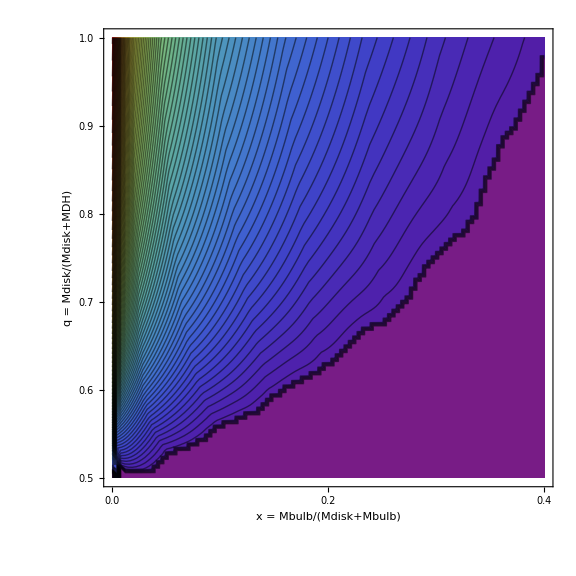

-Graphics-

```mathematica
pGR=ListContourPlot[GRTable,Contours->100,PlotRange->{All,All,{zmin,zmax}},ColorFunction->"Rainbow",FrameLabel->{ay,ax},BaseStyle->basestyleplot,LabelStyle->labelstyleplot,PlotLegends->Placed[BarLegend[{(ColorData["Rainbow"][#]&),{zmin,zmax}},LegendLabel->"Growth rate",Method->{FrameStyle->axstyle,TicksStyle->tickstyle,Ticks->{{0,"0"},(*{0.25,""},{0.5,"0.5"},{0.75,""},*){1,""},(*{1.25,""},{1.5,"1.5"},{1.75,""},*){2,""},{3,""},{4,""},{5,"5"},{6,""},{7,""},{8,""},{9,""},{10,"10"},{11,""},{12,""},{13,""},{14,""},{15,"15"},{16,""},{17,""},{18,""},{19,""},{20,"20"},{21,""},{22,""},{23,""},{24,""},{25,"25"},{26,""},{27,""},{28,""},{29,""},{30,"30"}}}],Above],ImageSize->imagesize,FrameTicks->{xticks,qticks},FrameStyle->{axstyle,axstyle,axstyle,axstyle},PlotRangePadding->None]
pGR=Rasterize[pGR,RasterSize->1000];
pDensGR=ListPlot3D[GRTable,PlotRange->{{xmin,xmax},{qmin,qmax},All},ColorFunction->"Rainbow",BaseStyle->basestyleplot,LabelStyle->labelstyleplot,ImageSize->imagesize,PlotRangePadding->None,AxesLabel->{ay,ax,"GR"},MeshFunctions->{#3&}];
pDensGR=Rasterize[pDensGR,RasterSize->1000]
```

#### Save data

```mathematica
Export["../graphs/growthRate_eps0_1.png",pGR]
Export["../graphs/growthRate3D_eps0_1.png",pDensGR]
```

../graphs/growthRate_eps0_1.png

../graphs/growthRate3D_eps0_1.png

## Rotation frequency associated with the fastest mode

#### Import data

#### Diffusion coefficients

```mathematica
(*tabqx=Import["../data/Dump_Growth_Rate_Rotation_eps0_1_precise.hf5",{"Datasets","tabqx"}];
tabRot=Import["../data/Dump_Growth_Rate_Rotation_eps0_1_precise.hf5",{"Datasets","tabRot"}]; *)
tabqx=Import["../data/Dump_Growth_Rate_Rotation_eps0_1.hf5",{"Datasets","tabqx"}];
tabRot=Import["../data/Dump_Growth_Rate_Rotation_eps0_1.hf5",{"Datasets","tabRot"}]; 

RotTable=Partition[{tabqx,tabRot}//Transpose//Flatten,3];
a=RotTable[[All,1]];
b=RotTable[[All,2]];
RotTable[[All,2]]=a;
RotTable[[All,1]]=b;
```

#### Plot data

```mathematica
(*Generic options for the plots.*)
fontname = "Didot";
fontsize = 12;
basestyleplot = {FontFamily -> fontname,FontSize->fontsize};
labelstyleplot = {FontFamily -> fontname, FontSize -> fontsize};
imagesize = Large;(*350;*)
(*Making the plot.*)
(*Range of the plot.*)
qmin = 0.5;
qmax =1.0;
xmin = 0.0;
xmax = 0.4;
zmin =0;
zmax = 3;
(*Axes of the plot.*)
ax = Row[{Style["q = ",fontname,fontsize],Style[FractionBox["Mdisk","Mdisk+MDH"]//DisplayForm,fontname,fontsize]}]
ay =  Row[{Style["x = ",fontname,fontsize],Style[FractionBox["Mbulb","Mdisk+Mbulb"]//DisplayForm,fontname,fontsize]}]
(*.*)
axstyle = {Black,Thickness[0.003]};
tickstyle = {Black,Thickness[0.003]};
(*.*)
qticks =  {{0,"0.0"},{0.1,""},{0.2,""},{0.3,""},{0.4,""},{0.5,"0.5"},{0.6,""},{0.7,""},{0.8,""},{0.9,""},{1.0,"1.0"}};
xticks =  {{0.0,"0.0"},{0.1,"0.1"},{0.2,""},{0.3,""},{0.4,""},{0.5,"0.5"},{0.6,""},{0.7,""},{0.8,""},{0.9,""},{1.0,"1.0"}};
zticks={1,2,3,4,5,6,7,8,9,10};
```

q = Mdisk/(Mdisk+MDH)

x = Mbulb/(Mdisk+Mbulb)

```mathematica
pRot=ListContourPlot[RotTable,Contours->100,PlotRange->{All,All,{zmin,zmax}},ColorFunction->"Rainbow",FrameLabel->{ay,ax},BaseStyle->basestyleplot,LabelStyle->labelstyleplot,PlotLegends->Placed[BarLegend[{(ColorData["Rainbow"][#]&),{zmin,zmax}},LegendLabel->"Rotation frequency",Method->{FrameStyle->axstyle,TicksStyle->tickstyle,Ticks->{{0,"0"},(*{0.25,""},{0.5,"0.5"},{0.75,""},*){1,""},(*{1.25,""},{1.5,"1.5"},{1.75,""},*){2,""},{3,""},{4,""},{5,"5"},{6,""},{7,""},{8,""}(*,{9,""},{10,"10"},{11,""},{12,""},{13,""},{14,""},{15,"15"},{16,""},{17,""}*)}}],Above],ImageSize->imagesize,FrameTicks->{qticks,xticks},FrameStyle->{axstyle,axstyle,axstyle,axstyle},PlotRangePadding->None]
pRot=Rasterize[pRot,RasterSize->1000];
pDensRot=ListPlot3D[RotTable,PlotRange->{{xmin,xmax},{qmin,qmax},{zmin,zmax}},ColorFunction->"Rainbow",BaseStyle->basestyleplot,LabelStyle->labelstyleplot,ImageSize->imagesize,PlotRangePadding->None,AxesLabel->{ay,ax,"GR"},MeshFunctions->{#3&}];
pDensRot=Rasterize[pDensRot,RasterSize->1000]
```

-Graphics-

-Graphics-

#### Save data

```mathematica
Export["../graphs/RotationFreq_eps0_1.png",pRot]
Export["../graphs/RotationFreq3D_eps0_1.png",pDensRot]
```

../graphs/RotationFreq_eps0_1.png

../graphs/RotationFreq3D_eps0_1.png